Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1 - 6 Euler for systems and second-order ODEs
Solve by the Euler’s method. Graph the solution in the y_1 y_2 -plane. Calculate the errors.

1.  y_1'[x]=2 y_1[x]-4y_2[x], y_2'[x]==y_1[x]-3 y_2[x], y_1[0]==3, y_2[0]==0

```mathematica
Clear["Global`*"]
```

If both functions that I use have the capability to solve a system of ODEs, that seems remarkable. The exact case is with

```mathematica
s1=DSolve[{y1'[x]==2 y1[x]-4y2[x], y2'[x]==y1[x]-3 y2[x], y1[0]==3, y2[0]==0},{y1,y2},x]
```

{{y1→Function[{x},ⅇ^(-2 x) (-1+4 ⅇ^(3 x))],y2→Function[{x},ⅇ^(-2 x) (-1+ⅇ^(3 x))]}}

```mathematica
p1=Plot[{y1[x]/.s1,y2[x]/.s1},{x,-1,4},PlotStyle->{{Blue,Thickness[0.008]},{RGBColor[0.8,0.3,0.2],Thickness[0.008]}}];
```

It’s particularly satisfying to see that the options which enhance accuracy and precision work as well for the dual equations as for the individual ones.

```mathematica
s2=NDSolve[{y1'[x]==2 y1[x]-4y2[x], y2'[x]==y1[x]-3 y2[x], y1[0]==3, y2[0]==0},{y1,y2},{x,-1,4},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->20]
```

{{y1→InterpolatingFunction[{{-1.0000000000000000000, 4.0000000000000000000}}, <>],y2→InterpolatingFunction[{{-1.0000000000000000000, 4.0000000000000000000}}, <>]}}

```mathematica
p2=Plot[{y1[x]/.s2,y2[x]/.s2},{x,-1,4},PlotStyle->{{White,Thickness[0.004]},{White,Thickness[0.004]}}];
```

The plots work exactly like one of the previous problems in section 21.1 or 21.2, only in duplicate.

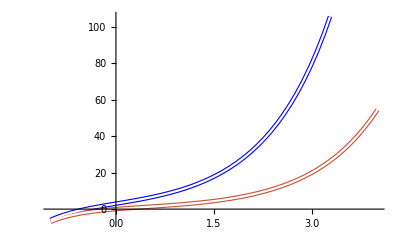

```mathematica
Show[p1,p2]
```

The values table can easily be adjusted to accommodate four functions. Everything adjusts and the accuracy between pairs of table columns seems to be 9S or better.

```mathematica
TableForm[Table[NumberForm[{y1[x]/.s1,y1[x]/.s2,y2[x]/.s1,y2[x]/.s2},{8,8}],{x,-1,4,0.4}]]
```

{{-5.91753830},{-5.91753830},{-7.02117670},{-7.02117670}}
{{-1.12487040},{-1.12487030},{-2.77130530},{-2.77130520}}
{{1.78309830},{1.78309830},{-0.67309394},{-0.67309394}}
{{4.21529100},{4.21529100},{0.55108271},{0.55108271}}
{{6.98728100},{6.98728100},{1.52092460},{1.52092460}}
{{10.73779200},{10.73779200},{2.58294650},{2.58294650}}
{{16.15999000},{16.15999000},{3.99438990},{3.99438990}}
{{24.17126600},{24.17126600},{6.02232370},{6.02232370}}
{{36.08777700},{36.08777600},{9.01273620},{9.01273610}}
{{53.84943600},{53.84943500},{13.45822100},{13.45822100}}
{{80.33966900},{80.33966800},{20.08305800},{20.08305800}}
{{119.85529000},{119.85529000},{29.96298600},{29.96298600}}
{{178.80424000},{178.80424000},{44.70068400},{44.70068400}}

3.  y''[x]+1/4 y[x]==0,y[0]==1, y'[0]==0

```mathematica
Clear["Global`*"]
```

This problem is not a system but rather a simple second order ODE.

```mathematica
s1=DSolve[{y''[x]+1/4 y[x]==0, y[0]==1, y'[0]==0},y,x]
```

{{y→Function[{x},Cos[x/2]]}}

```mathematica
p1=Plot[y[x]/.s1,{x,-5,5},PlotStyle->{RGBColor[0.3,0.7,0.2],Thickness[0.008]}];
```

```mathematica
s2=NDSolve[{y''[x]+1/4 y[x]==0, y[0]==1, y'[0]==0},y,{x,-5,5},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->20]
```

{{y→InterpolatingFunction[{{-5.0000000000000000000, 5.0000000000000000000}}, <>]}}

The plot is delivered as expected. Once the equation is solved, everything that follows is exactly like first order.

```mathematica
p2=Plot[{y[x]/.s2},{x,-5,5},PlotStyle->{White,Thickness[0.004]}];
```

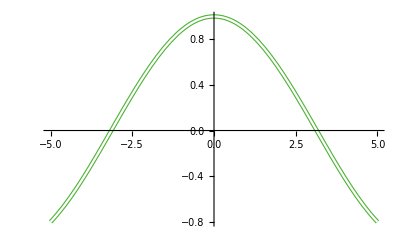

```mathematica
Show[p1,p2]
```

The table of comparison values between functions has the close equivalence of a number of the recent problem solutions.

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s2},{8,8}],{x,-5,5,0.8}]]
```

{{-0.80114362},{-0.80114362}}
{{-0.50484610},{-0.50484610}}
{{-0.12884449},{-0.12884449}}
{{0.26749883},{0.26749883}}
{{0.62160997},{0.62160997}}
{{0.87758256},{0.87758256}}
{{0.99500417},{0.99500417}}
{{0.95533649},{0.95533649}}
{{0.76484219},{0.76484219}}
{{0.45359612},{0.45359612}}
{{0.07073720},{0.07073720}}
{{-0.32328957},{-0.32328957}}
{{-0.66627602},{-0.66627602}}

5.  y''[x] - y[x] == x, y[0] == 1, y'[0] == -2

A problem consisting of another second order ODE.

```mathematica
Clear["Global`*"]
```

Mathematica can solve this one in closed form

```mathematica
s1=DSolve[{y''[x]-y[x]==x,y[0]==1,y'[0]==-2},y,x]
```

{{y→Function[{x},-ⅇ^-x (-1+ⅇ^x x)]}}

```mathematica
p1=Plot[y[x]/.s1,{x,-5,5},PlotStyle->{RGBColor[0.7,0.2,0.7],Thickness[0.008]}];
```

as well as in numerical approximation.

```mathematica
s2=NDSolve[{y''[x]-y[x]==x,y[0]==1,y'[0]==-2},y,{x,-5,5},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->20]
```

{{y→InterpolatingFunction[{{-5.0000000000000000000, 5.0000000000000000000}}, <>]}}

```mathematica
p2=Plot[{y[x]/.s2},{x,-5,5},PlotStyle->{White,Thickness[0.004]}];
```

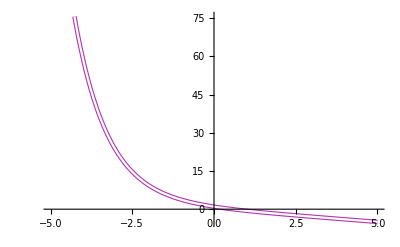

```mathematica
Show[p1,p2]
```

And modified with suitable enhancers, the table comparison shows very good correlation between values of the two functions.

```mathematica
TableForm[Table[NumberForm[{y[x]/.s1,y[x]/.s2},{8,8}],{x,-5,5,0.8}]]
```

{{153.41316000},{153.41316000}}
{{70.88633100},{70.88633100}}
{{33.36410000},{33.36410000}}
{{16.06373800},{16.06373800}}
{{7.84964750},{7.84964750}}
{{3.71828180},{3.71828180}}
{{1.42140280},{1.42140280}}
{{-0.05118836},{-0.05118836}}
{{-1.15340300},{-1.15340300}}
{{-2.08919680},{-2.08919680}}
{{-2.95021290},{-2.95021290}}
{{-3.77762920},{-3.77762920}}
{{-4.58994820},{-4.58994820}}

7 - 10 RK for systems
Solve by the classical RK

7.  The ODE in problem 5. By what factor did the error decrease?

The error is so miniscule that in my opinion there is no need to try to get it to decrease.

9.  The system in problem 1.

The system in problem 1 has been solved definitively, I believe.

11.  Pendulum equation
y’’[x] + Sin[y[x]] == 0, y[π] == 0, y’[π] == 1, as a system, 20 steps. How does your result fit into figure 93 in section 4.5?

```mathematica
Clear["Global`*"]
```

I think I see how this could be treated as a system, with sine handled as a separate function. But it was easier to try to solve it monolithically first, and it worked. The text answer page does not show a result for the solution function y[x]. I am only assuming that Mathematica got it right.

```mathematica
eqn={y''[x]+Sin[y[x]]==0,y[π]==0,y'[π]==1}
```

{Sin[y[x]]+y''[x]==0,y[π]==0,y'[π]==1}

```mathematica
s1=Simplify[DSolve[{y''[x]+Sin[y[x]]==0,y[π]==0,y'[π]==1},y,x]]
```

{{y→Function[{x},2 JacobiAmplitude[1/2 (-π+x),4]]}}

I’m not sure if the following constitutes a successful check of the DSolve activities, but it may.

```mathematica
eqn/.s1
```

{{-2 JacobiCN[1/2 (-π+x),4] JacobiSN[1/2 (-π+x),4]+Sin[2 JacobiAmplitude[1/2 (-π+x),4]]==0,True,True}}

```mathematica
p1=Plot[y[x]/.s1,{x,-5,5},PlotStyle->{RGBColor[0.8,0.7,0.2],Thickness[0.008]}];
```

```mathematica
s2=NDSolve[{y''[x]+Sin[y[x]]==0,y[π]==0,y'[π]==1},y,{x,-5,5},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->20]
```

{{y→InterpolatingFunction[{{-5.0000000000000000000, 5.0000000000000000000}}, <>]}}

```mathematica
p2=Plot[{y[x]/.s2},{x,-5,5},PlotStyle->{White,Thickness[0.004]}];
```

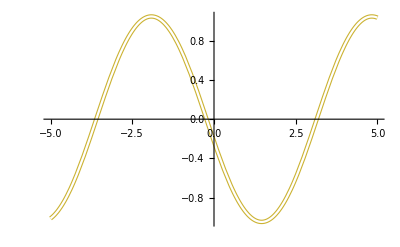

```mathematica
Show[p1,p2]
```

The Simplify command I used in the definition of s1 did not do as I had hoped. It did not eliminate the phantom imaginary Arg from the function values of s1. These would show up in the table without the exclusionary Re command on s1. I feel fairly confident in stripping Arg, since all the Arg values are far less than default Chop. The comparison of the remaining real parts shows an agreeably close equivalence.

```mathematica
TableForm[Table[NumberForm[{Re[y[x]]/.s1,y[x]/.s2},{8,8}],{x,-5,5,0.8}]]
```

{{-1.01161520},{-1.01161520}}
{{-0.56405817},{-0.56405817}}
{{0.20005255},{0.20005255}}
{{0.84859892},{0.84859892}}
{{1.04140840},{1.04140840}}
{{0.69811386},{0.69811386}}
{{-0.02990360},{-0.02990360}}
{{-0.74057792},{-0.74057792}}
{{-1.04584740},{-1.04584740}}
{{-0.81332394},{-0.81332394}}
{{-0.14112048},{-0.14112048}}
{{0.61277079},{0.61277079}}
{{1.02486590},{1.02486590}}